#### Two equations in two variables

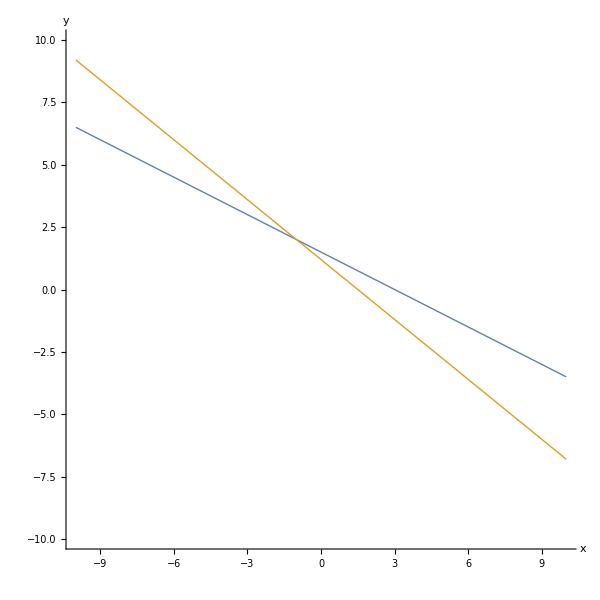

```mathematica
ContourPlot[
{x+2y== 3,4x+5y==6},{x,-10,10},{y,-10,10},
ContourStyle->Thick,Frame->False,Axes->True,AxesStyle->Thick,
BaseStyle->{15,"Courier",Bold},AxesLabel->Automatic,
ImageSize->600]
```

```mathematica
ContourPlot3D[
{x+2y== 3,4x+5y==6},{x,-10,10},{y,-10,10},{z,-10,10},
ContourStyle->Thick,Mesh->False,Axes->True,AxesStyle->Thick,
BaseStyle->{15,"Courier",Bold},AxesLabel->Automatic,
ImageSize->600]
```

-Graphics3D-

#### 3 equations in 3 variables

```mathematica
ContourPlot3D[
{x+2y+z==12,2x-y+z==1,x+y-3z==-4},{x,-10,10},{y,-10,10},{z,-10,10},
ContourStyle->{{Blue,Thick},{Green,Thick},{Red,Thick}},Mesh->False,Axes->True,AxesStyle->Thick,
BaseStyle->{15,"Courier",Bold},AxesLabel->Automatic,
ImageSize->600]
```

-Graphics3D-

```mathematica
ContourPlot3D[
{6x+7y+8z==8,4x+5y+9z==0,2x-2y+7z==7},{x,-10,10},{y,-10,10},{z,-10,10},
ContourStyle->{{Blue,Thick},{Green,Thick},{Red,Thick}},Mesh->False,Axes->True,AxesStyle->Thick,
BaseStyle->{15,"Courier",Bold},AxesLabel->Automatic,
ImageSize->600]
```

-Graphics3D-

```mathematica
Clear[x,y,z]
Solve[{6x+7y+8z==8,4x+5y+9z==0,2x-2y+7z==7},{x,y,z}]
Solve[{x+2y+z==12,2x-y+z==1,x+y-3z==-4},{x,y,z}]
```

{{x→45/8,y→-9/4,z→-5/4}}

{{x→1,y→4,z→3}}